# CNN Project

## Review

Baoxiang Pan
2017.7.13

## Data

Precipitation

#### NCEP_Reanalysis

```mathematica
precip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]];
	mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]];	
	Table[Import["prate.sfc.gauss."<>ToString[year]<>".nc",{"Datasets","prate"}][[;;,21;;31,126;;133]],
		{year,1948,2006}]];
```

#### ECMWF_Reanalysis

#### CPC_Gauge

```mathematica
SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
year=1948;
precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
mlat=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lat"}][[48;;]];
mlon=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lon"}][[21;;65]];
precip=precip /. x_/; x< 0 ->nan;
precip[[;;,32;;,26;;]]=nan;
Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	   t,tt},
	t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
	tt=Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t];
	Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt]];
```

```mathematica
precip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	mlat=Import["precip.V1.0.1948.nc",{"Datasets","lat"}][[48;;]];
	mlon=Import["precip.V1.0.1948.nc",{"Datasets","lon"}][[21;;65]];
	tt=Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	       t},
			t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
			Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t]];
	Table[Block[{precip},
		precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip],{year,1948,2006}]];
```

Sea Level Pressure

#### NCEP_Reanalysis

```mathematica
SLP=Block[{mlat,mlon},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
	mlat=Import["slp.1948.nc",{"Datasets","lat"}][[13;;28]];
	mlon=Import["slp.1948.nc",{"Datasets","lon"}][[89;;99]];
	Table[Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}][[;;,13;;28,89;;99]],
		{year,1948,2006}]];
```

```mathematica
Dimensions[precip[[1]]]
Dimensions[SLP[[1]]]
```

{1464,11,8}

{1464,16,11}

#### ECMWF_Reanalysis

## Network Structure

```mathematica
winter=Flatten[Table[{Range[1+year*365*4,60*4+year*365*4],Range[270*4+year*365*4,365*4+year*365*4]},{year,0,58}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,36555,86099,86100,86101,86102,86103,86104,86105,86106,86107,86108,86109,86110,86111,86112,86113,86114,86115,86116,86117,86118,86119,86120,86121,86122,86123,86124,86125,86126,86127,86128,86129,86130,86131,86132,86133,86134,86135,86136,86137,86138,86139,86140}
 |  |  |  |

```mathematica
Precip=Block[{m=Mean[Flatten[precip,1]]},
	Map[10000*Flatten[#-m]&,Flatten[precip,1]]][[winter]];
Slp=Block[{m=Mean[Flatten[SLP,1]]},
	Map[{#-m}/350.&,Flatten[SLP,1]]][[winter]];
Dimensions[Precip]
Dimensions[Slp]
{Precip,Slp}=Block[{tempt=RandomSample[Table[{Precip[[i]],Slp[[i]]},{i,Length[Slp]}]]},
	{Map[#[[1]]&,tempt],Map[#[[2]]&,tempt]}];
Dimensions[Precip]
Dimensions[Slp]
```

{36639,88}

{36639,1,16,11}

{36639,88}

{36639,1,16,11}

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2,1],
						 ConvolutionLayer[1, 3], 
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 (*DropoutLayer[0.05],*)
						 BatchNormalizationLayer[],
						 300,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.1],
						 BatchNormalizationLayer[],
						 150,
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[],
						 88,
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[]},  
					"Input" -> {1,16,11}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[Slp]*0.7]
```

25647

```mathematica
ann=NetTrain[CNN,
	Slp[[1;;ptraining]]->Precip[[1;;ptraining]],
	ValidationSet->Table[Slp[[i]]->Precip[[i]],{i,ptraining,Length[Slp]}],
	Method->"ADAM",
	BatchSize->200,
	MaxTrainingRounds -> 2000]
```

NetChain[]

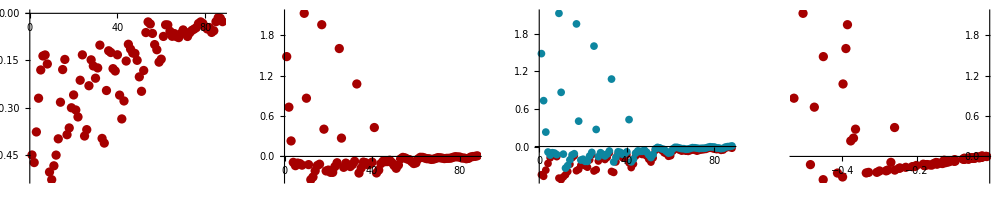

```mathematica
day=184;
GraphicsRow[{ListPlot[Precip[[day]],PlotRange->Full],
			 ListPlot[ann@Slp[[day]],PlotRange->Full],
			 ListPlot[{Precip[[day]], ann@Slp[[day]]},PlotRange->Full],
			 ListPlot[Transpose[{Precip[[day]], ann@Slp[[day]]}],PlotRange->Full]},ImageSize->1000]
```

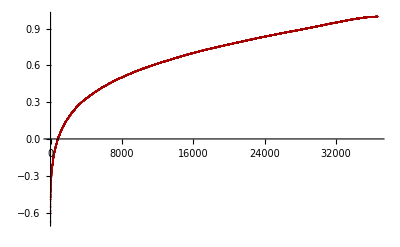

```mathematica
test=Table[Correlation[Precip[[day]], ann@Slp[[day]]],{day,1,Length[Slp]}];
ListPlot[Sort[test]]
```

```mathematica
Position[test,Min[test[[1;;1700]]]]
```

{{184}}

```mathematica
Mean[test]
```

0.514688

```mathematica
SetDirectory["/Users/lambda/Documents/S2S/Results"];
Export["ANN.txt",ann]
```

ANN.txt

## Network Structure

```mathematica
Precip=Block[{tempt=Map[Select[Flatten[#],NumberQ]&,Flatten[precip,1]],m,v},
	 v=Sqrt[Variance[tempt]];
	 m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[Precip]
```

{21550,1450}

```mathematica
SLP=Block[{tempt=Flatten[slp,1],m,v},
	v=Sqrt[Variance[tempt]];
	m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[SLP]
```

{21550,16,11}

```mathematica
winter=Flatten[Table[{Range[1+year*365,90+year*365],Range[275+year*365,365+year*365]},{year,0,58}]];
```

```mathematica
Precip=Precip[[winter]];
SLP=SLP[[winter]];
```

```mathematica
CNN=NetInitialize[NetChain[{ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2,1],
						 ConvolutionLayer[1, 3], 
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.5],
						 BatchNormalizationLayer[],
						 900,
						 ElementwiseLayer[Ramp],
						 900,
						 ElementwiseLayer[Ramp],
						 1450,
						 BatchNormalizationLayer[]},  
					"Input" -> {1,16,11}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[SLP]*0.7]
```

7475

```mathematica
ann = NetTrain[CNN,
	Map[{#}&,SLP[[1;;ptraining]]] -> Precip[[1;;ptraining]],
	ValidationSet->Table[{SLP[[i]]}->Precip[[i]],{i,ptraining,Length[SLP]}],
	Method->"ADAM",
	BatchSize->200,
	MaxTrainingRounds -> 2000]
```

NetChain[]

```mathematica
Dimensions[SLP]
```

{10679,16,11}

```mathematica
simu=Table[ann@{SLP[[day]]},{day,Length[SLP]}];
```

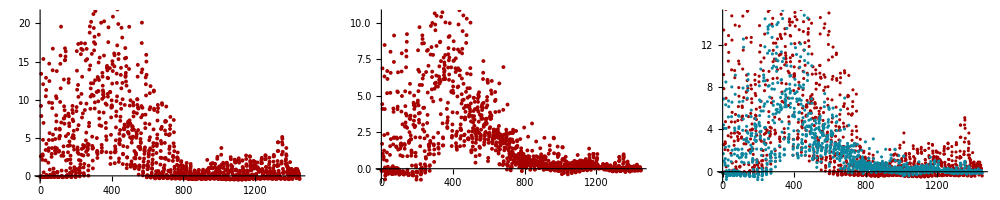

```mathematica
day=3419;
GraphicsRow[{ListPlot[Precip[[day]]],ListPlot[ann@{SLP[[day]]}],ListPlot[{Precip[[day]],ann@{SLP[[day]]}}]},
	ImageSize->1000]
```

```mathematica
test=Table[Correlation[ann@{SLP[[day]]},Precip[[day]]],{day,Length[SLP]}];
```

```mathematica
MinMax[test]
```

{-0.656667,0.973372}

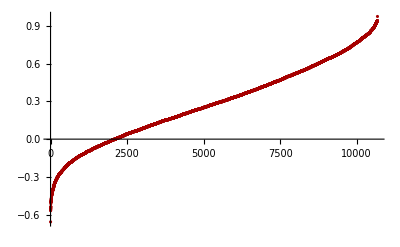

```mathematica
ListPlot[Sort[test]]
```

```mathematica
Position[test,Max[test[[1;;365*10]]]]
```

{{3419}}

### Second level section heading

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.